#### Lagrange interpolation KZ

```mathematica
fun[fun_,x0_,h_,n_]:=Module[{x1={},x},x=x0;
Do[AppendTo[x1,x];x+=h,n+1];Product[(t-i+1),{i,1,n+1}]/(n!)*Sum[((-1)^(n-k)Binomial[n,k])/(t-k)fun[x1⟦k⟧],{k,1,n+1}]]
```

#### Test 1

```mathematica
pol=fun[#^3&,1,1,3];
```

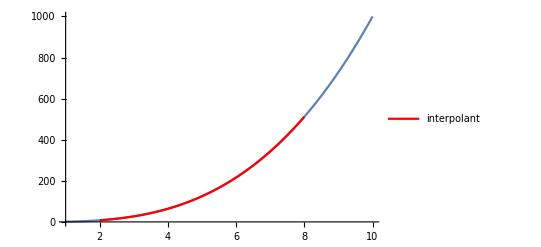

```mathematica
Show[{Plot[k^3,{k,1,10}],Plot[pol/.t->k,{k,2,8},PlotStyle->Red,PlotLegends->{"interpolant"}]}]
```

#### Test 2

```mathematica
pol1=fun[Cos[#]&,1,1,5];
```

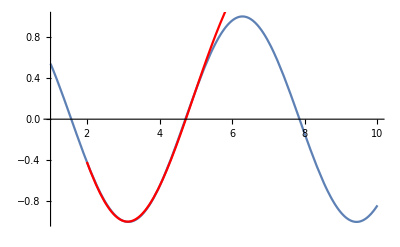

```mathematica
Show[{Plot[Cos[k],{k,1,10}],Plot[pol1/.t->k,{k,2,8},PlotStyle->Red]}]
```

```mathematica
pol2=fun[Cos[#]&,1,1,10];
```

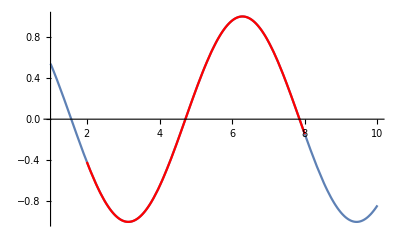

```mathematica
Show[{Plot[Cos[k],{k,1,10}],Plot[pol2/.t->k,{k,2,8},PlotStyle->Red]}]
```